```mathematica
Quit[];
```

# MGPT_CLPT (August, 2018) Compute CLPT correlation function for matter and tracers

Authors:

Mario Alberto Rodriguez-Meza (ININ, Mexico)
marioalberto.rodriguez@inin.gob.mx

Alejandro Aviles (Conacyt/ININ, Mexico)
alejandro.aviles.conacyt@inin.gob.mx, avilescervantes@gmail.com

Paper references: 
For CLPT:                arXiv:1209.0780  (But we use the resummation of arXiv:1506.05264 )
For CLPT in MG:    arXiv:1705.10719, arXiv: 1809.xxxxx

If you use this code, please cite the reference arXiv: 1809.xxxxx. You may also want to cite the other references listed above.

RUN:  shift-enter on the biggest right bracket →
It runs in about 10-20 minutes.

Specify range of output evenly distributed in Delta r:

```mathematica
(*Specify the range of output, evenly distributed in Delta r *)
INPUTFILE="qfunctions_nb.dat";
OUTPUTFILE="CorrelationFunction_nb.dat";
```

0.808081

## Initialize

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["NumericalDifferentialEquationAnalysis`"] (*To compute Gauss-Legendre integration points*)
```

## Import q-functions

```mathematica
qfunctT=Import[INPUTFILE,"Data"];
Dimensions[%]
xiL=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,14]]}]];
XL=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,2]]}]];
YL=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,3]]}]];
Xloop=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,4]]}]];
Yloop=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,5]]}]];
V=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,6]]}]];
T=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,7]]}]];
X10=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,8]]}]];
Y10=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,9]]}]];
UL=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,10]]}]];
Uloop=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,11]]}]];
U11=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,12]]}]];
U20=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,13]]}]];
Lapxi=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,15]]}]];
nabla4xi=Interpolation[Transpose[{qfunctT[[All,1]],qfunctT[[All,16]]}]];
qmax=Max[qfunctT[[All,1]]]
qmin=Min[qfunctT[[All,1]]]
U[q_]:=UL[q]+Uloop[q]
```

## Define scalar functions

A_{ij}= fX  \delta_{ij} + hY \hat{q}_i \hat{q}_j
q_i = {qx, qy, qz}
qx = q mu
qy=0
qz=q Sqrt[1 - mu^2]
r_i = {0, 0, r }

```mathematica
fX[q_]:= 1/XL[q]
hY[q_]:=-YL[q]/(XL[q]XL[q]+XL[q]YL[q])
BDet[ff_,hh_]:=ff Sqrt[ff+hh];
preMZA[q_,r_,mu_,fx_,hy_]:=q^2 (2 Pi)^(-1/2) BDet[fx,hy]Exp[-0.5(hy (q-mu r)^2+fx (q^2-2 mu q r+r^2))];
MZA[q_,r_,mu_]:=preMZA[q,r,mu,fX[q],hY[q]];


AijGij[q_,r_,mu_,ft_,ht_,Xloopt_,Yloopt_]:=-(ft^2 (q^2-2 mu q r+r^2)+ht (-1+ht (q-mu r)^2)+ft (-3+2 ht (q-mu r)^2)) Xloopt-(ft+ht) (-1+(ft+ht) (q-mu r)^2) Yloopt;
WijkGammaijk[q_,r_,mu_,ft_,ht_,Vt_,Tt_]:=(ft+ht) (-q+mu r) ((ft+ht) (-3+(ft+ht) (q-mu r)^2) Tt+3 (ft^2 (q^2-2 mu q r+r^2)+ht (-3+ht (q-mu r)^2)+ft (-5+2 ht (q-mu r)^2)) Vt);
qigi[q_,r_,mu_,ft_,ht_]:=(ft+ht) (q-mu r)
qiqjGij[q_,r_,mu_,ft_,ht_]:=-(ft+ht) (-1+(ft+ht) (q-mu r)^2)


MA[q_,r_,mu_]:=-0.5MZA[q,r,mu]AijGij[q,r,mu,fX[q],hY[q],Xloop[q],Yloop[q]]
MW[q_,r_,mu_]:=+1/6.MZA[q,r,mu]WijkGammaijk[q,r,mu,fX[q],hY[q],V[q],T[q]]

MU[q_,r_,mu_]:=-2.MZA[q,r,mu]U[q] qigi[q,r,mu,fX[q],hY[q]]
MA10[q_,r_,mu_]:=-MZA[q,r,mu]AijGij[q,r,mu,fX[q],hY[q],X10[q],Y10[q]]
MxiR[q_,r_,mu_]:=MZA[q,r,mu]xiL[q]
MLapxiR[q_,r_,mu_]:=MZA[q,r,mu]Lapxi[q]
Mnabla4xiR[q_,r_,mu_]:=MZA[q,r,mu]nabla4xi[q]
MUU[q_,r_,mu_]:=-MZA[q,r,mu]UL[q]UL[q]qiqjGij[q,r,mu,fX[q],hY[q]]
MU11[q_,r_,mu_]:=- MZA[q,r,mu]U11[q] qigi[q,r,mu,fX[q],hY[q]]
MU20[q_,r_,mu_]:=- MZA[q,r,mu]U20[q] qigi[q,r,mu,fX[q],hY[q]]
MxiR2[q_,r_,mu_]:=0.5MZA[q,r,mu]xiL[q]xiL[q]
MUxiR[q_,r_,mu_]:=-2.MZA[q,r,mu]UL[q] qigi[q,r,mu,fX[q],hY[q]]xiL[q]

M10[q_,r_,mu_]:=MU[q,r,mu]+MA10[q,r,mu]  (* b1*)
M10L[q_,r_,mu_]:=MU[q,r,mu]  (* b1*)
M10loop[q_,r_,mu_]:=MA10[q,r,mu]  (* b1*)
M01[q_,r_,mu_]:= MUU[q,r,mu]+MU20[q,r,mu]    (* b2*)
M20[q_,r_,mu_]:=MxiR[q,r,mu]+MUU[q,r,mu]+MU11[q,r,mu] (* b1^2*)
M20L[q_,r_,mu_]:=MxiR[q,r,mu](* b1^2*)
M20loop[q_,r_,mu_]:=MUU[q,r,mu]+MU11[q,r,mu] (* b1^2*)
M02[q_,r_,mu_]:=MxiR2[q,r,mu]   (* b2^2*)
M11[q_,r_,mu_]:=MUxiR[q,r,mu]   (* b1*b2*)
```

## Zeldovich Approximation Correlation Function

```mathematica
Nx=128;
tGL=GaussianQuadratureWeights[Nx,-1,1];
muGL=tGL[[All,1]];
wGL=tGL[[All,2]];

xiZAT={};

Do[
r=rr;
xip=0;xiB=0;
qprev=0.5;
Do[
q=qq;
deltaq=q-qprev;
(*Print[q,", ",qprev,", ",deltaq];*)
Do[
mu=muGL[[muii]];
w=wGL[[muii]];
mza=MZA[q,r,mu];
xiB=xiB+w*mza;
,{muii,1,Nx}];
If[qq==1,xiA=xiB];
xip=xip+(xiA+xiB)/2.*deltaq;
(*Print[xip];*)
xiA=xiB;
xiB=0;
qprev=q;
,{qq,1,250,1}];
xip=xip-1;
xiZAT=Append[xiZAT,{rr,xip}]
,{rr,rRange[[1]],rRange[[2]],rRange[[3]]}]//AbsoluteTiming
```

## A, W and bias components

```mathematica
qT=Table[qq,{qq,3,240,1}];
preqT=Table[qq*0.5,{qq,1,5,1}];
qT=Join[preqT,qT];
sizeqT=Dimensions[qT][[1]]


Nx=64;
tGL=GaussianQuadratureWeights[Nx,-1,1];
muGL=tGL[[All,1]];
wGL=tGL[[All,2]];
(*qmaxinteg=1000;
qmininteg=1;*)

(*SetSharedVariable[xi10LT,xi10loopT,xi20LT,xi20loopT,xi01T,xi02T,xi11T,xiAT,xiWT]*)
xi10LT={};
xi10loopT={};
xi20LT={};
xi20loopT={};
xi01T={};
xi02T={};
xi11T={};
xiAT={};
xiWT={};
xiLapxiT={};
xinabla4xiT={};

Do[
ta=AbsoluteTime[];
r=rr;
xiAp=0;xiAB=0;
xiWp=0;xiWB=0;
xi10Lp=0;xi10LB=0;
xi10loopp=0;xi10loopB=0;
xi20Lp=0;xi20LB=0;
xi20loopp=0;xi20loopB=0;
xi01p=0;xi01B=0;
xi02p=0;xi02B=0;
xi11p=0;xi11B=0;
xiLapxip=0;xiLapxiB=0;
xinabla4xip=0;xinabla4xiB=0;
qprev=0.00001;
Do[
q=qT[[qii]];
deltaq=q-qprev;
Do[
mu=muGL[[muii]];
w=wGL[[muii]];

mA=MA[q,r,mu];
mW=MW[q,r,mu];
m10L=M10L[q,r,mu];
m10loop=M10loop[q,r,mu];
m20L=M20L[q,r,mu];
m20loop=M20loop[q,r,mu];
m01=M01[q,r,mu];
m02=M02[q,r,mu];
m11=M11[q,r,mu];
mLapxi=MLapxiR[q,r,mu];
mnabla4xi=Mnabla4xiR[q,r,mu];

xiAB=xiAB+w*mA;
xiWB=xiWB+w*mW;
xi10LB=xi10LB+w*m10L;
xi10loopB=xi10loopB+w*m10loop;
xi20LB=xi20LB+w*m20L;
xi20loopB=xi20loopB+w*m20loop;
xi01B=xi01B+w*m01;
xi02B=xi02B+w*m02;
xi11B=xi11B+w*m11;
xiLapxiB=xiLapxiB+w*mLapxi;
xinabla4xiB=xinabla4xiB+w*mnabla4xi;

,{muii,1,Nx}];

If[qii==1,xiAA=xiAB];
If[qii==1,xiWA=xiWB];
If[qii==1,xi10LA=xi10LB];
If[qii==1,xi20LA=xi20LB];
If[qii==1,xi10loopA=xi10loopB];
If[qii==1,xi20loopA=xi20loopB];
If[qii==1,xi01A=xi01B];
If[qii==1,xi02A=xi02B];
If[qii==1,xi11A=xi11B];
If[qii==1,xiLapxiA=xiLapxiB];
If[qii==1,xinabla4xiA=xinabla4xiB];

xiAp=xiAp+(xiAA+xiAB)/2.*deltaq;
xiWp=xiWp+(xiWA+xiWB)/2.*deltaq;
xi10Lp=xi10Lp+(xi10LA+xi10LB)/2.*deltaq;
xi10loopp=xi10loopp+(xi10loopA+xi10loopB)/2.*deltaq;
xi20Lp=xi20Lp+(xi20LA+xi20LB)/2.*deltaq;
xi20loopp=xi20loopp+(xi20loopA+xi20loopB)/2.*deltaq;
xi01p=xi01p+(xi01A+xi01B)/2.*deltaq;
xi02p=xi02p+(xi02A+xi02B)/2.*deltaq;
xi11p=xi11p+(xi11A+xi11B)/2.*deltaq;
xiLapxip=xiLapxip+(xiLapxiA+xiLapxiB)/2.*deltaq;
xinabla4xip=xinabla4xip+(xinabla4xiA+xinabla4xiB)/2.*deltaq;

xiAA=xiAB;xiAB=0;
xiWA=xiWB;xiWB=0;
xi10LA=xi10LB;xi10LB=0;
xi10loopA=xi10loopB;xi10loopB=0;
xi20LA=xi20LB;xi20LB=0;
xi20loopA=xi20loopB;xi20loopB=0;
xi01A=xi01B;xi01B=0;
xi02A=xi02B;xi02B=0;
xi11A=xi11B;xi11B=0;
xiLapxiA=xiLapxiB;xiLapxiB=0;
xinabla4xiA=xinabla4xiB;xinabla4xiB=0;

qprev=q;
,{qii,1,sizeqT}];

xiAT=Append[xiAT,{rr,xiAp}];
xiWT=Append[xiWT,{rr,xiWp}];
xi10LT=Append[xi10LT,{rr,xi10Lp}];
xi10loopT=Append[xi10loopT,{rr,xi10loopp}];
xi20LT=Append[xi20LT,{rr,xi20Lp}];
xi20loopT=Append[xi20loopT,{rr,xi20loopp}];
xi01T=Append[xi01T,{rr,xi01p}];
xi02T=Append[xi02T,{rr,xi02p}];
xi11T=Append[xi11T,{rr,xi11p}];
xiLapxiT=Append[xiLapxiT,{rr,xiLapxip}];
xinabla4xiT=Append[xinabla4xiT,{rr,xinabla4xip}];

(*Print["r=",rr,", xiA=",xiAp,", xiW=",xiWp,", xi10L=",xi10Lp,", xi10loop=",xi10loopp,", xi20L=",xi20Lp,", xi20loop=",xi20loopp,", xi0l=",xi01p,", xi02=",xi02p,", xi11=",xi11p,", xiLapxi=",xiLapxip,", xinabla4xi=",xinabla4xip,",  time= ",AbsoluteTime[]-ta];*)

,{rr,rRange[[1]],rRange[[2]],rRange[[3]]}]//AbsoluteTiming
```

{1202.32047,Null}

## Export CorrelationFunction.dat

```mathematica
sizeExpT=Dimensions[xiZAT][[1]];
exportT=Table[{xiZAT[[ii,1]],xiL[xiZAT[[ii,1]]],xiZAT[[ii,2]],xiAT[[ii,2]],xiWT[[ii,2]],xi10LT[[ii,2]],xi10loopT[[ii,2]],xi20LT[[ii,2]],xi20loopT[[ii,2]],xi01T[[ii,2]],xi02T[[ii,2]],xi11T[[ii,2]],xiLapxiT[[ii,2]],xinabla4xiT[[ii,2]]},{ii,1,sizeExpT}];
Dimensions[%]
Export[OUTPUTFILE,exportT]
```

{100,14}

CorrelationFunctionN1_nb.dat

# Plots

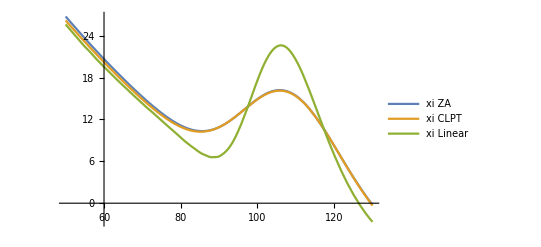

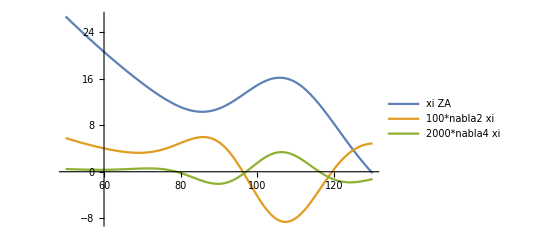

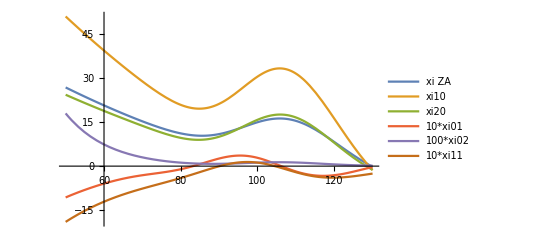

```mathematica
rini=rRange[[1]];
rfin=rRange[[2]];
xiA=Interpolation[xiAT];
xiW=Interpolation[xiWT];
xiZA=Interpolation[xiZAT];
xiCLPT[r_]:=xiZA[r]+xiA[r]+xiW[r]

xi10L=Interpolation[xi10LT];
xi10loop=Interpolation[xi10loopT];
xi20L=Interpolation[xi20LT];
xi20loop=Interpolation[xi20loopT];
xi01=Interpolation[xi01T];
xi02=Interpolation[xi02T];
xi11=Interpolation[xi11T];

xi10[r_]:=xi10L[r]+xi10loop[r]
xi20[r_]:=xi20L[r]+xi20loop[r]

xiLapxi=Interpolation[xiLapxiT];
xinabla4xi=Interpolation[xinabla4xiT];

Plot[{r^2xiZA[r],r^2xiCLPT[r],r^2xiL[r]},{r,rini,rfin},PlotLegends->{"xi ZA","xi CLPT","xi Linear"}]
Plot[{r^2xiZA[r],100r^2xiLapxi[r],2000r^2xinabla4xi[r]},{r,rini,130},PlotLegends->{"xi ZA","100*nabla2 xi","2000*nabla4 xi"}]

Plot[{r^2 xiZA[r],r^2 xi10[r],r^2 xi20[r],10*r^2 xi01[r],100*r^2 xi02[r],10*r^2 xi11[r]},{r,rini,rfin},PlotLegends->{"xi ZA","xi10 ","xi20", "10*xi01", "100*xi02", "10*xi11"}]
```